## Лабораторная работа №5 Брич.М.Н.

## Задание 1

На основе проделанных выше вычислений подберите примеры, подтверждающие справедливость следующих утверждений :

Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

Введение дополнительных пробелов не изменяет результата вычислений.

```mathematica
3               5
```

15

```mathematica
3                   /                          2
```

3/2

Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
17^(1/2)
```

√17

```mathematica
3/7
```

3/7

Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
17.^(1/2)
```

4.12311

```mathematica
3/7.
```

0.428571

Для изменения стандартного порядка выполнения операции используются круглые скобки.

```mathematica
3                  (3 +        3)
```

18

## Задание 2

С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200] (*N - численное приближение, N[a,b], где b - количество знаков после запятой*)
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%] (* % - предыдущий результат*)
```

200.

Найдите приближенное значение числа e^(Pi*√163) точностью до 40 значащих цифр. Вычислите, на сколько полученный результат отличается от ближайшего к нему целого числа. Для стандартного округления чисел в системе используется Round[x]

```mathematica
N[E^(Pi*Sqrt[163]),40] (* Вычисляем приближённое значение с точность до 40 значащих цифр *)
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[%] - % (* Округляем предыдущее значение и отнимаем неокругленное, тем самым получаем расстояние до ближайшего целого*)
```

7.499274028×10^-13

Вычислите

```mathematica
(10 √((10.8 10^3)/300)+4)^(1/3)
```

4.

```mathematica
(10^-24*10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражения: 5 > 3; 5 < 2; и посмотрите, что выдает математика при их обработке. Затем определите, справедливо или нет равенство Pi^e>e^Pi. Найдите численные значения левой и правой частей неравенства и убедитесь в правильности полученного результата.

```mathematica
5 > 3
5 < 2
```

True

False

```mathematica
N[Pi^E, 10]
N[E^Pi, 10]
```

22.45915772

23.14069263

```mathematica
Pi^E>E^Pi
```

False

## Задание 3 Решить уравнения и системы уравнений

-Graphics-

```mathematica
NSolve[√(x+2)+4 x==4, x] (* NSolve - численное решение уравнения. NSolve[a,b] - где b - переменная для нахождения *)
(* В ответе получаем действительное число *)
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
(* В ответе получаем 1 действительное число, 2 комплексных *)
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

-Graphics-

```mathematica
(* NSolve также поддерживает и системы уравнений *)
```

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
(* В ответе получаем комплексные числа *)
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
(* В ответе получаем комплексные числа *)
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумайте уравнение или систему полиномиальных уравнений и найдите ее численное решение

```mathematica
NSolve[{x^2+ 1==0, 2y+2x== 0}, {x,y}]
```

{{x→0.-1. ⅈ,y→0.+1. ⅈ},{x→0.+1. ⅈ,y→0.-1. ⅈ}}

## Задание 4

Используя  функцию FindRoot, найти решения следующих уравнений 
Для решения произвольных уравнений и их систем используется функция FindRoot, она находит только одна численное решение при каждом обращении к ней

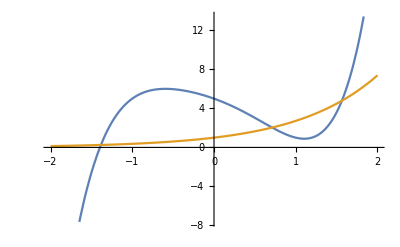

```mathematica
Plot[{x^5 - 2*x^2 - 3*x + 5,  Exp[x]},{x, -2,2}] (* Строим график левой и правой частей уравнения, чтобы найти приближённые значения корней *)
```

```mathematica
(* Как видно из графика выше, приближенные значения корней == -1.5, 0.8, 1.6 по х, поэтому используем эти значения в функции FindRoot*)
(* FindRoot[a,{x,b}] == а-выражение, b-стартовая позиция поиска ближайшего корня *)
(* FindRoot находит корни уравнения быстрее, т.к. мы точно указываем ему примерное нахождение корня, NDSolve ищет все корни, поэтому теоритечески может работать бесконечно *)
FindRoot[x^5 - 2*x^2 - 3*x + 5 ==  Exp[x],{x,-1.5}] 
FindRoot[x^5 - 2*x^2 - 3*x + 5 ==  Exp[x],{x,0.8}]
FindRoot[x^5 - 2*x^2 - 3*x + 5 ==  Exp[x],{x,1.6}]
```

{x→-1.38364}

{x→0.711247}

{x→1.56426}

## Задание 5

Найдите решение следующего дифференциального уравнения на заданном отрезке

```mathematica
sol = NDSolve[{y''[x] + y'[x]*Tan[x]+ 3 *y[x] ==0, y[0] == 0, y'[0] == 2}, y, {x,0,5}]  (*NDSolve - численное решение ДУ*)
(* Получаем решение в виде правил подстановки для искомой функции. Интерполяционнуя функция - функция, полученная путём интерполяции (нахождение неизвестных промежуточных значений по некоторому набору известных значений), т.е. к примеру {{0,0}{1,1}{2,3}{3,4}{4,3}{5,0}} *)
```

{{y→InterpolatingFunction[…]}}

```mathematica
(* Теперь из этих найденных значений строим график этой функции, так мы видим где лежат корни уравнений *)
```

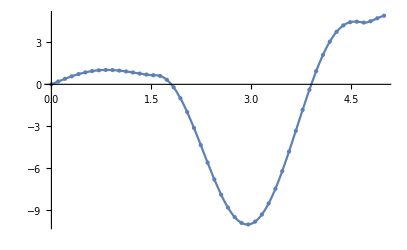

```mathematica
Plot[y[x]/.sol,{x,0,5}, Mesh->Full] (* /. - заменить все *)
```

```mathematica
(* По условию нужно найти корни уравнений y(x)=0, т.е. те корни, которые пересекают ось x. Указываем их приближённые значения, получаем точное значение *)
```

```mathematica
sol1 = FindRoot[(y[x]/.sol)==0,{x,0}]
sol2 = FindRoot[(y[x]/.sol)==0,{x,1.8}]
sol3 = FindRoot[(y[x]/.sol)==0,{x,3.9}]
```

{x→0.}

{x→1.80132}

{x→3.90596}

```mathematica
(* Вычисляем значения производных в найденных точках *)
```

```mathematica
D[y[x]/.sol,x]/.sol1 (* D - дифференцировать (найти производную) при х = sol1 *)
D[y[x]/.sol,x]/.sol2
D[y[x]/.sol,x]/.sol3
(* Получаем действительные числа, знак указывает убывает функция или возрастает. *)
```

{2.}

{-5.68927}

{13.3568}

```mathematica
(* Найденная функция имеет около точки х = 3 локальный минимум, приравниваем производную этой функции к нулю и решая полученное уравнение, получаем точное значение х *)
```

```mathematica
sol4 = FindRoot[D[y[x]/.sol,x]==0,{x,3}] (* Выполняем поиск корня при помощи FindRoot, в качестве выражения берем производную == 0, эта точк *)
```

{x→2.94512}

```mathematica
(* Соответствующее значение функции равно: *)
y[x]/.sol/.sol4
```

{-10.0398}

```mathematica
(* Теперь с помощью функции FindMinimum находим локальный минимум функции *)
```

```mathematica
FindMinimum[y[x]/.sol,{x,3}] (* Данная функция имеет похожую структуру с FindRoot, результат == результату в предыдущем пункте *)
```

{-10.0398,{x→2.94512}}

## Задание 6

Задайте произвольные численные значения параметров a, b, c, d, e в следующих зависимостях-Graphics-
В данном задании функционально изменяются координаты тела. Используя функцию Table, определите список численных данных, каждый элемент которого содержит два соответствующих элемента (x, y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение del y.

```mathematica
a=-1;b=3;c=1;d=-3;e=2; (* задаём начальные численные значения вышеуказанных параметров *)
(* Table[{x,y},{x,startPoint,endPoint,step}] в качестве y будет наше выражение, умноженное на погрешность (1 + случайное значение от -0.1 до 0.1) *)
dat1 = Table[{x, (a+b x+c x^2+d x^3+e x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,2,0.1}] 
dat2 = Table[{x, (a+b 3 x+c Sin[x]+d Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,2,0.1}]
dat3 = Table[{x, (a+b x+c Sin[x]+d Cos[2 x])(1+Random[Real,{-0.1,0.1}])},{x,0,2,0.1}]
dat4 = Table[{x, (a Sin[x]+b Cos[x]+c Sin[2 x]+d Cos[2 x])(1+Random[Real,{-0.1,0.1}])},{x,0,2,0.1}]
```

{{0.,-1.04427},{0.1,-0.658383},{0.2,-0.385037},{0.3,-0.0763009},{0.4,0.197315},{0.5,0.502819},{0.6,0.717554},{0.7,1.07732},{0.8,1.26582},{0.9,1.50921},{1.,2.13571},{1.1,2.42058},{1.2,2.71631},{1.3,3.86927},{1.4,4.73445},{1.5,5.23355},{1.6,7.44896},{1.7,8.70938},{1.8,11.6156},{1.9,14.9198},{2.,17.3007}}

{{0.,-3.94701},{0.1,-3.25495},{0.2,-2.13383},{0.3,-0.934403},{0.4,0.211853},{0.5,1.31872},{0.6,2.43633},{0.7,3.91708},{0.8,4.97587},{0.9,5.71037},{1.,7.5404},{1.1,8.57061},{1.2,9.72055},{1.3,10.6541},{1.4,11.5245},{1.5,13.4468},{1.6,15.4324},{1.7,16.5283},{1.8,15.9146},{1.9,19.3599},{2.,19.0177}}

{{0.,-3.6458},{0.1,-3.40872},{0.2,-2.83673},{0.3,-2.06598},{0.4,-1.38227},{0.5,-0.61824},{0.6,0.272981},{0.7,1.32011},{0.8,2.29721},{0.9,3.43328},{1.,4.13166},{1.1,4.65297},{1.2,5.70422},{1.3,6.05134},{1.4,7.6683},{1.5,7.6981},{1.6,7.10923},{1.7,8.68039},{1.8,7.9143},{1.9,8.5456},{2.,7.53864}}

{{0.,0.},{0.1,0.144631},{0.2,0.357817},{0.3,0.623807},{0.4,0.980108},{0.5,1.30512},{0.6,1.69839},{0.7,1.96713},{0.8,2.25172},{0.9,2.91889},{1.,2.92983},{1.1,2.99335},{1.2,2.83143},{1.3,2.79718},{1.4,2.57538},{1.5,2.53621},{1.6,2.01592},{1.7,1.21939},{1.8,0.608822},{1.9,-0.167281},{2.,-0.862017}}

Изобразите полученные точки на координатной плоскости

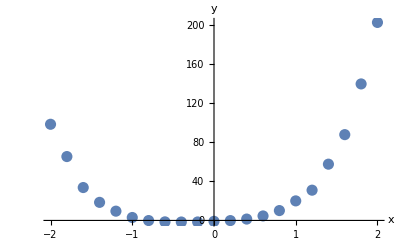

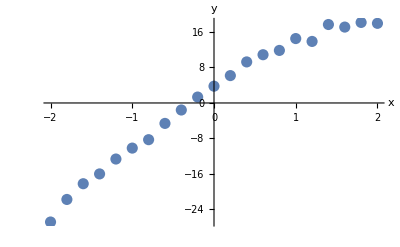

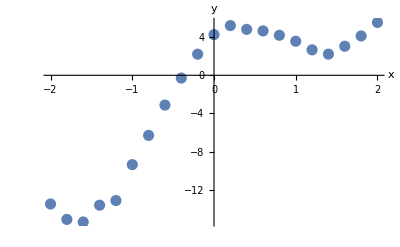

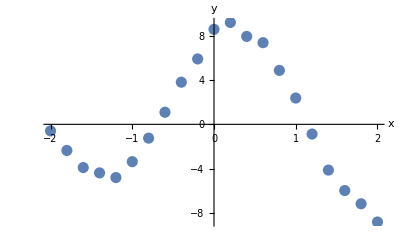

```mathematica
(* У нас нету численных данных коэфициентов зависимости, а есть только таблицы численных данных. Чтобы видеть эту зависимоть отметим эти точки на графице. ListPlot - диаграмма разброса данных *)
p1 = ListPlot[dat1,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
p2 = ListPlot[dat2,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
p3 = ListPlot[dat3,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
p4 = ListPlot[dat4,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
(* Fit - функция для нахождения наилучших значений коэффициентов выражения
Fit[data, vars, x] - data-численные данные, vars-список функций, линейная комбинация которых должна аппроксимировать искомую зависимость. x-независимая переменная *)
y1 = Fit[dat1,{1, x, x^2,x^3,x^4}, x]
y2 = Fit[dat2,{1,x,Sin[x],Cos[x]}, x]
y3 = Fit[dat3,{1,x,Sin[x],Cos[2 x]}, x]
y4 = Fit[dat4,{Sin[x],Cos[x],Sin[2 x],Cos[2 x]}, x]
```

-1.0377+3.31391 x+0.521613 x^2-2.9897 x^3+2.12111 x^4

-1.13569+9.34401 x-2.96739 Cos[x]+0.784789 Sin[x]

-0.482148+3.01413 x-3.22419 Cos[2 x]+0.293588 Sin[x]

3.04918 Cos[x]-3.02951 Cos[2 x]-1.01659 Sin[x]+0.900658 Sin[2 x]

На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

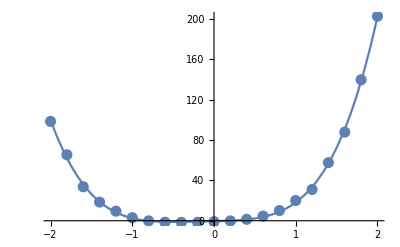

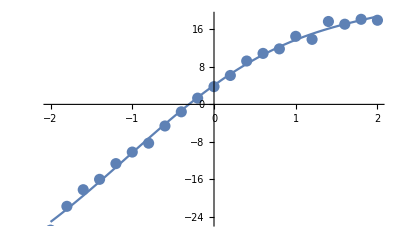

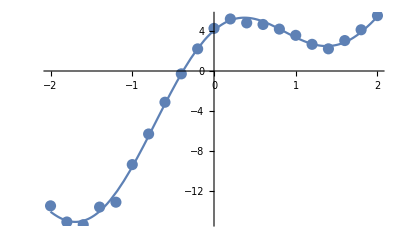

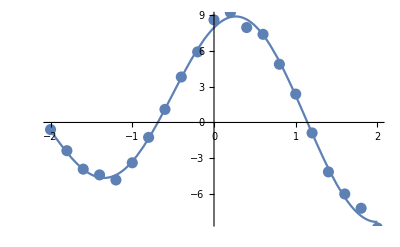

```mathematica
(* Plot - строим график функции *)
p11 := Plot[{y1},{x,-2,2}]
p21 := Plot[{y2},{x,-2,2}]
p31 := Plot[{y3},{x,-2,2}]
p41 := Plot[{y4},{x,-2,2}]
(* Показываем одновременно график функции, и диаграмму разброса данных при помощи Show, чтобы посмотреть, насколько хорошо найденные кривые проходят через точки *)
Show[p11,p1]
Show[p21,p2]
Show[p31,p3]
Show[p41,p4]
```